```mathematica
data=Import["C:\\Users\\Naman Taggar\\Desktop\\interactions.csv"];
```

```mathematica
rules=DeleteDuplicatesBy[Rule@@@data[[2;;,{2,3}]],Sort[List@@#]&];
```

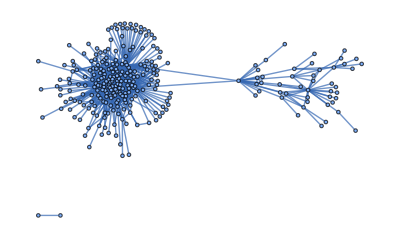

```mathematica
G=Graph[rules,DirectedEdges->False]
```

Two servers connected via me.

Now we find communities in this graph

```mathematica
coms=Subgraph[G,#]&/@FindGraphCommunities[G];
```

```mathematica
Length[coms]
```

8

there are 8 communities of

```mathematica
VertexCount/@coms
```

{84,73,47,41,23,7,5,2}

members respectively.

```mathematica
EdgeCount/@coms
```

{294,111,68,99,28,6,4,1}

These communities have this many interactions in them. Graph densities:

```mathematica
GraphDensity/@coms//N
```

{0.0843373,0.0422374,0.0629047,0.120732,0.110672,0.285714,0.4,1.}

It shows how dense a community is. Denseness ≈ 1 means a community is very much connected (almost same as the connected graph).

```mathematica
MeanClusteringCoefficient/@coms//N
```

{0.419611,0.097304,0.255601,0.247139,0.0729723,0.,0.,0.}

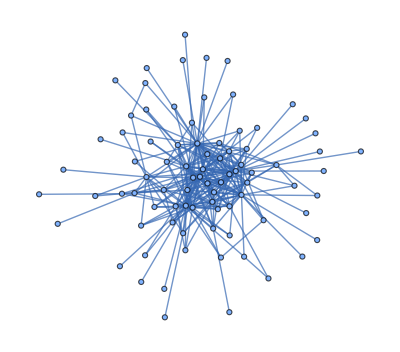

```mathematica
coms[[1]]
```

```mathematica
Pick[VertexList[G],DegreeCentrality[G],Max[DegreeCentrality[G]]]
```

{1180937923365961881}

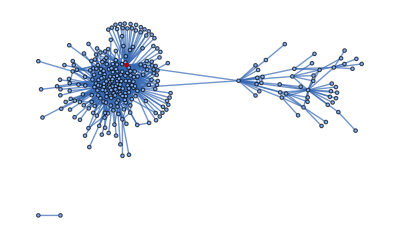

```mathematica
HighlightGraph[G,%]
```

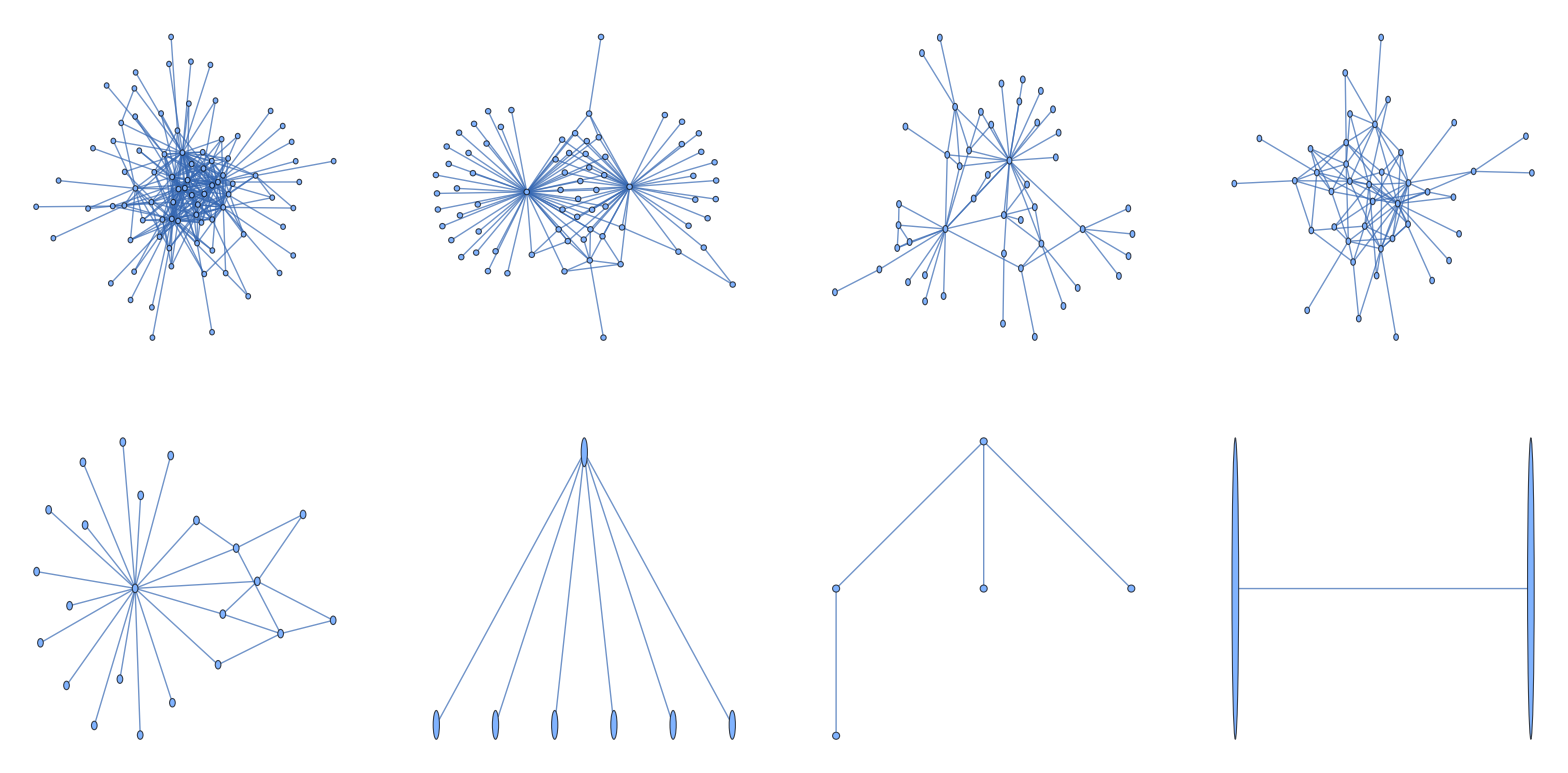

```mathematica
GraphicsGrid[Partition[coms,4,4]]
```